# Single-atom in cavity LASER

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumAliases[];
```

### Three-level atom and up to ten-photon restriction

## Defining Operators

```mathematica
DefineOperatorOnKets[Subscript[a, OverHat[1]],{|Subscript[0, OverHat[1]]⟩->0,Table[|Subscript[n, OverHat[1]]⟩ ->  √n|Subscript[(n-1), OverHat[1]]⟩,{n,1,10}]}//Flatten];
```

```mathematica
DefineOperatorOnKets[SuperDagger[Subscript[a, OverHat[1]]], {Table[|Subscript[n, OverHat[1]]⟩ ->  √(n+1)|Subscript[(n+1), OverHat[1]]⟩,{n,0,9}],|Subscript[10, OverHat[1]]⟩->0}//Flatten];
```

## Identification of Density Matrix Elements

```mathematica
Basis=Table[{|Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]⟩,|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩,|Subscript[n, OverHat[1]],Subscript[3, OverHat[2]]⟩},{n,0,10}]//Flatten;
```

```mathematica
BasisAdj=Table[{⟨Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]|,⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|,⟨Subscript[n, OverHat[1]],Subscript[3, OverHat[2]]|},{n,0,10}]//Flatten;
```

```mathematica
Calling=Table[Table[BasisAdj[[i]]·ρ̂[t]·Basis[[j]]-> ρ[i,j][t],{j,1,33}],{i,1,33}]//Flatten;
```

## Master Equation term by term

```mathematica
ρ̂'[1][t]=g·SuperDagger[Subscript[a, OverHat[1]]]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[2][t]=-g·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·Subscript[a, OverHat[1]]·ρ̂[t];
```

```mathematica
ρ̂'[3][t]=-g·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[4][t]=g·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·Subscript[a, OverHat[1]];
```

```mathematica
ρ̂'[5][t]=2·κ·Subscript[a, OverHat[1]]·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]];
```

```mathematica
ρ̂'[6][t]=-κ·SuperDagger[Subscript[a, OverHat[1]]]·Subscript[a, OverHat[1]]·ρ̂[t];
```

```mathematica
ρ̂'[7][t]=-κ·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]]·Subscript[a, OverHat[1]];
```

```mathematica
ρ̂'[8][t]=Γ/2·2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

```mathematica
ρ̂'[9][t]=-Γ/2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[10][t]=-Γ/2·ρ̂[t]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[11][t]=γ12/2·2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[12][t]=-γ12/2·|Subscript[2, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[13][t]=-γ12/2·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[14][t]=γ13/2·2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[15][t]=-γ13/2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[16][t]=-γ13/2·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

```mathematica
ρ̂'[17][t]=γ23/2·2·|Subscript[2, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[18][t]=-γ23/2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[19][t]=-γ23/2·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

## Equations of motion of density matrix elements

```mathematica
Eqs1=Table[Table[ρ[j,i]'[t],{i,1,33}],{j,1,33}]//Flatten;
```

```mathematica
SepEq1=Table[Table[Table[BasisAdj[[j]]·ρ̂'[k][t]·Basis[[i]],{k,1,19}],{j,1,33}],{i,1,33}];
```

```mathematica
Eqs2=Table[Table[Sum[SepEq1[[j]][[i]][[m]],{m,1,19}],{j,1,33}],{i,1,33}]//Flatten;
```

```mathematica
Equations1={Table[Eqs1[[o]]== Eqs2[[o]],{o,1,1089}]}/.Calling//Flatten;
```

## Results

## Dynamic Results

```mathematica
33*33
```

1089

```mathematica
γ12=1;γ13=0;γ23=0.5;g=1;κ=0.01;Γ=1;
```

```mathematica
Equations1;
```

. Initial Conditions: |Ψ(t=0)⟩= |0_OverHat[1],1_OverHat[2]⟩

```mathematica
Eqs3=Table[Table[ρ[j,i][0],{i,1,33}],{j,1,33}]//Flatten;
```

```mathematica
Eqs4={1,Table[0 p,{p,2,1089}]}//Flatten;
```

```mathematica
InitialConditions1={Table[Eqs3[[q]]== Eqs4[[q]],{q,1,1089}]}//Flatten;
```

```mathematica
list1={Equations1,InitialConditions1}//Flatten;
```

```mathematica
sol1=NDSolve[list1,Table[Table[ρ[j,i],{i,1,33}],{j,1,33}]//Flatten,{t,0,100}];
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

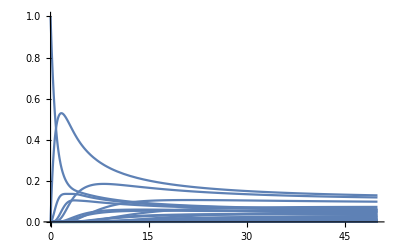

```mathematica
Plot[Table[ρ[i,i][t],{i,1,33}]/.sol1,{t,0,50},PlotRange-> All]
```

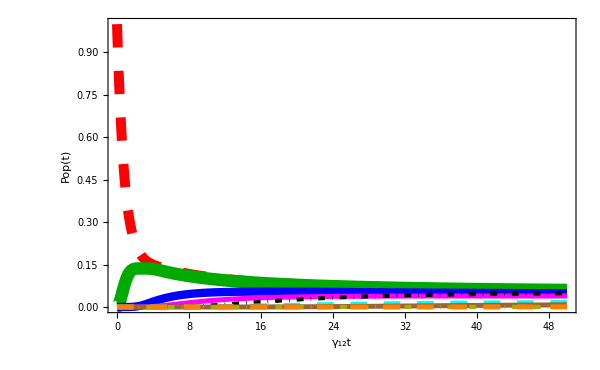

```mathematica
ShowLegend[Plot[{ρ[1,1][t]/.sol1,ρ[2,2][t]/.sol1,ρ[7,7][t]/.sol1,ρ[8,8][t]/.sol1,ρ[15,15][t]/.sol1,ρ[16,16][t]/.sol1,ρ[24,24][t]/.sol1,ρ[32,32][t]/.sol1,ρ[33,33][t]/.sol1},{t,0,50},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]},{Darker[Green],Thickness[0.015],CapForm["Round"],Dashing[{1*^-10,0.014 2,0.014 2,0.014 2}]},{Thickness[0.01],Blue},{Thickness[0.006],Magenta},{Thickness[0.005],DotDashed,Black},{Dashing[0.02],Thickness[0.006],Cyan},{Thickness[0.006],Brown},{Thickness[0.005],DotDashed,Darker[Yellow]},{Dashing[0.02],Thickness[0.006],Orange}},Frame->True,FrameLabel->{"γ_12t","Pop(t)"},FrameStyle->Directive[Black, AbsoluteThickness[1.5]],BaseStyle->{FontWeight->"Bold",FontSize->20},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->16]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]],Line[{{0,0.5},{4,0.5}}]}],Style["| 0_1, 1_2⟩",Bold,16]},
{Graphics[{Darker[Green],Thickness[0.1],CapForm["Round"],Dashing[{1*^-10,0.014 10,0.014 10,0.014 10}],Line[{{0,0.5},{4,0.5}}]}],Style["| 0_1, 2_2⟩",Bold,16]},{Graphics[{Blue,AbsoluteThickness[5],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 2_1, 1_2⟩",Bold,16]},{Graphics[{Magenta,AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 2_1, 2_2⟩",Bold,16]},{Graphics[{Black, DotDashed,AbsoluteThickness[2],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 4_1, 3_2⟩",Bold,16]},{Graphics[{Cyan,Dashing[0.2],AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 5_1, 1_2⟩",Bold,16]},{Graphics[{Brown,AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 7_1, 3_2⟩",Bold,16]},{Graphics[{Darker[Yellow], DotDashed,AbsoluteThickness[2],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 10_1, 2_2⟩",Bold,16]},{Graphics[{Orange,Dashing[0.2],AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 10_1, 3_2⟩",Bold,16]}},LegendPosition->{-0.19,-0.13},LegendBackground->White,LegendBorder->Black,LegendShadow->None,LegendSize->{0.46,0.62},LegendTextSpace->1.2},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 10",Bold,25]}},LegendPosition->{0.45,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.25,0.1},LegendTextSpace->50},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["(d)",Bold,32]}},LegendPosition->{-0.65,0.37},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.25,0.1},LegendTextSpace->20}]
```

Comment: Since for up to 5 photon restriction there are 18 basis so just plotted 9 of the states’ population.

#### Plotting sum of diagonal elements to check the normalization as we’ll use it as the 37th equation in the steady-state solution (37th equation was needed)

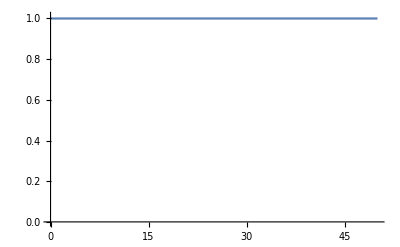

```mathematica
Plot[Sum[ρ[i,i][t],{i,1,33}]/.sol1,{t,0,50},PlotRange-> {{0,50},{0,1.01}}]
```

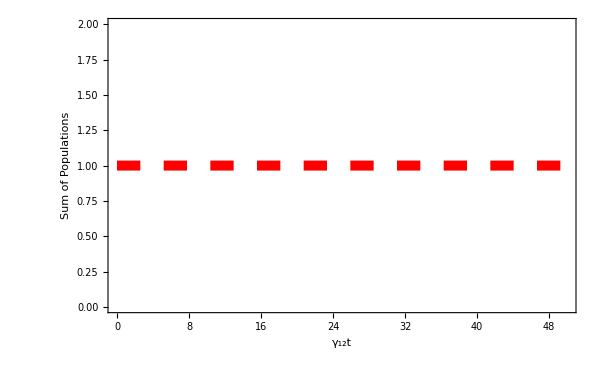

```mathematica
Plot[Sum[ρ[i,i][t],{i,1,33}]/.sol1,{t,0,50},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"γ_12t","Sum of Populations"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]
```

Comment: Since in the following where finding the steady-state solution we impose the normalization condition therefore as a check we confirmed the normalization above.

## Steady-state Results

```mathematica
Clear[Γ,γ12,γ13,γ23,g,κ]
```

```mathematica
Set1=Table[Table[ρ[j,i]'[t]-> 0,{i,1,33}],{j,1,33}]//Flatten;
```

```mathematica
SSEquations1={Equations1/.Set1,1== Sum[ρ[i,i][t],{i,1,33}]}//Flatten;
```

```mathematica
Set2={Table[Table[ρ[j,i][t],{i,1,33}],{j,1,33}]}//Flatten;
```

```mathematica
γ12=1;γ13=0;γ23=0.5;g=1 ;κ=0.01 ;
```

```mathematica
SSEquations1;
```

```mathematica
SSsol[n_]:=Solve[SSEquations1/.Γ-> n,Set2]//Flatten
```

Comment: Its turns out for up to five photon case, the symbolic solution to steady-state equations takes more than 5 minutes (I don’t know how many minutes it will take as the code was still running). Therefore, I followed the above method where I give all parameters except Γ and then make a table of solutions for each Γ value and use it to plot quantities of interest.

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
MeanPhoton0=Sum[Sum[n⟨Subscript[n, OverHat[1]],Subscript[i, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[i, OverHat[2]]⟩,{n,0,10}],{i,1,3}]/.Calling
```

ρ[4,4][t]+ρ[5,5][t]+ρ[6,6][t]+2 ρ[7,7][t]+2 ρ[8,8][t]+2 ρ[9,9][t]+3 ρ[10,10][t]+3 ρ[11,11][t]+3 ρ[12,12][t]+4 ρ[13,13][t]+4 ρ[14,14][t]+4 ρ[15,15][t]+5 ρ[16,16][t]+5 ρ[17,17][t]+5 ρ[18,18][t]+6 ρ[19,19][t]+6 ρ[20,20][t]+6 ρ[21,21][t]+7 ρ[22,22][t]+7 ρ[23,23][t]+7 ρ[24,24][t]+8 ρ[25,25][t]+8 ρ[26,26][t]+8 ρ[27,27][t]+9 ρ[28,28][t]+9 ρ[29,29][t]+9 ρ[30,30][t]+10 ρ[31,31][t]+10 ρ[32,32][t]+10 ρ[33,33][t]

```mathematica
MeanPhoton1=Table[ρ[4,4][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[5,5][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[6,6][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton2=Table[2ρ[7,7][t]/.SSsol[Γ],{Γ,0,100}]+Table[2ρ[8,8][t]/.SSsol[Γ],{Γ,0,100}]+Table[2ρ[9,9][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton3=Table[3ρ[10,10][t]/.SSsol[Γ],{Γ,0,100}]+Table[3ρ[11,11][t]/.SSsol[Γ],{Γ,0,100}]+Table[3ρ[12,12][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton4=Table[4ρ[13,13][t]/.SSsol[Γ],{Γ,0,100}]+Table[4ρ[14,14][t]/.SSsol[Γ],{Γ,0,100}]+Table[4ρ[15,15][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton5=Table[5ρ[16,16][t]/.SSsol[Γ],{Γ,0,100}]+Table[5ρ[17,17][t]/.SSsol[Γ],{Γ,0,100}]+Table[5ρ[18,18][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton6=Table[6ρ[19,19][t]/.SSsol[Γ],{Γ,0,100}]+Table[6ρ[20,20][t]/.SSsol[Γ],{Γ,0,100}]+Table[6ρ[21,21][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton7=Table[7ρ[22,22][t]/.SSsol[Γ],{Γ,0,100}]+Table[7ρ[23,23][t]/.SSsol[Γ],{Γ,0,100}]+Table[7ρ[24,24][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton8=Table[8ρ[25,25][t]/.SSsol[Γ],{Γ,0,100}]+Table[8ρ[26,26][t]/.SSsol[Γ],{Γ,0,100}]+Table[8ρ[27,27][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton9=Table[9ρ[28,28][t]/.SSsol[Γ],{Γ,0,100}]+Table[9ρ[29,29][t]/.SSsol[Γ],{Γ,0,100}]+Table[9ρ[30,30][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton10=Table[10ρ[31,31][t]/.SSsol[Γ],{Γ,0,100}]+Table[10ρ[32,32][t]/.SSsol[Γ],{Γ,0,100}]+Table[10ρ[33,33][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
MeanPhoton=MeanPhoton1+MeanPhoton2+MeanPhoton3+MeanPhoton4+MeanPhoton5+MeanPhoton6+MeanPhoton7+MeanPhoton8+MeanPhoton9+MeanPhoton10;
```

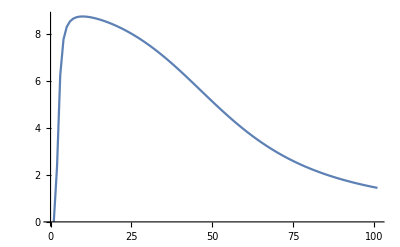

```mathematica
Nplot =ListLinePlot[MeanPhoton,PlotRange->All]
```

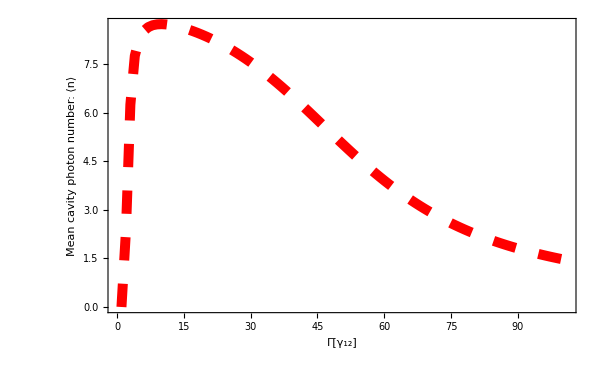

```mathematica
ShowLegend[Show[ListLinePlot[MeanPhoton,PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Γ[γ_12]","Mean cavity photon number: ⟨n⟩"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 10",Bold,25]}},LegendPosition->{0.45,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.24,0.1},LegendTextSpace->50}]
```

```mathematica
Ndata = Cases[Nplot, Line[p_]:>p,Infinity]//Flatten
MeanPhoton20=Sum[Sum[n^2⟨(Subscript[n, OverHat[1]]),Subscript[i, OverHat[2]]|·ρ̂[t]·|(Subscript[n, OverHat[1]]),Subscript[i, OverHat[2]]⟩,{n,0,10}],{i,1,3}]/.Calling
MeanPhoton21=Table[ρ[4,4][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[ρ[5,5][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[ρ[6,6][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton22=Table[2^2ρ[7,7][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[2^2ρ[8,8][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[2^2ρ[9,9][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton23=Table[3^2ρ[10,10][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[3^2ρ[11,11][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[3^2ρ[12,12][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton24=Table[4^2ρ[13,13][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[4^2ρ[14,14][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[4^2ρ[15,15][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton25=Table[5^2ρ[16,16][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[5^2ρ[17,17][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[5^2ρ[18,18][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton26=Table[6^2ρ[19,19][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[6^2ρ[20,20][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[6^2ρ[21,21][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton27=Table[7^2ρ[22,22][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[7^2ρ[23,23][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[7^2ρ[24,24][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton28=Table[8^2ρ[25,25][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[8^2ρ[26,26][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[8^2ρ[27,27][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton29=Table[9^2ρ[28,28][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[9^2ρ[29,29][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[9^2ρ[30,30][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton210=Table[10^2ρ[31,31][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[10^2ρ[32,32][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[10^2ρ[33,33][t]/.SSsol[Γ],{Γ,0,100,2}];
MeanPhoton2=MeanPhoton21+MeanPhoton22+MeanPhoton23+MeanPhoton24+MeanPhoton25+MeanPhoton26+MeanPhoton27+MeanPhoton28+MeanPhoton29+MeanPhoton210;
```

{1.,-1.08469×10^-16,2.,2.33232,3.,6.25122,4.,7.7612,5.,8.2936,6.,8.52902,7.,8.64641,8.,8.70601,9.,8.73293,10.,8.73926,11.,8.73151,12.,8.71343,13.,8.68734,14.,8.65471,15.,8.6165,16.,8.57338,17.,8.52579,18.,8.47403,19.,8.41831,20.,8.35876,21.,8.29547,22.,8.22849,23.,8.15786,24.,8.0836,25.,8.0057,26.,7.92417,27.,7.83901,28.,7.75025,29.,7.65789,30.,7.56198,31.,7.46255,32.,7.35968,33.,7.25346,34.,7.14399,35.,7.03139,36.,6.91584,37.,6.79749,38.,6.67655,39.,6.55325,40.,6.42781,41.,6.30051,42.,6.17161,43.,6.04141,44.,5.9102,45.,5.77828,46.,5.64597,47.,5.51357,48.,5.38139,49.,5.24973,50.,5.11886,51.,4.98907,52.,4.86062,53.,4.73374,54.,4.60867,55.,4.4856,56.,4.36472,57.,4.2462,58.,4.13016,59.,4.01674,60.,3.90602,61.,3.7981,62.,3.69302,63.,3.59084,64.,3.49157,65.,3.39524,66.,3.30183,67.,3.21134,68.,3.12374,69.,3.03898,70.,2.95704,71.,2.87785,72.,2.80136,73.,2.7275,74.,2.65622,75.,2.58744,76.,2.52109,77.,2.45709,78.,2.39538,79.,2.33587,80.,2.27849,81.,2.22316,82.,2.16982,83.,2.11839,84.,2.06879,85.,2.02097,86.,1.97484,87.,1.93034,88.,1.88741,89.,1.84599,90.,1.80601,91.,1.76742,92.,1.73016,93.,1.69417,94.,1.65941,95.,1.62582,96.,1.59336,97.,1.56198,98.,1.53163,99.,1.50227,100.,1.47387,101.,1.44638}

ρ[4,4][t]+ρ[5,5][t]+ρ[6,6][t]+4 ρ[7,7][t]+4 ρ[8,8][t]+4 ρ[9,9][t]+9 ρ[10,10][t]+9 ρ[11,11][t]+9 ρ[12,12][t]+16 ρ[13,13][t]+16 ρ[14,14][t]+16 ρ[15,15][t]+25 ρ[16,16][t]+25 ρ[17,17][t]+25 ρ[18,18][t]+36 ρ[19,19][t]+36 ρ[20,20][t]+36 ρ[21,21][t]+49 ρ[22,22][t]+49 ρ[23,23][t]+49 ρ[24,24][t]+64 ρ[25,25][t]+64 ρ[26,26][t]+64 ρ[27,27][t]+81 ρ[28,28][t]+81 ρ[29,29][t]+81 ρ[30,30][t]+100 ρ[31,31][t]+100 ρ[32,32][t]+100 ρ[33,33][t]

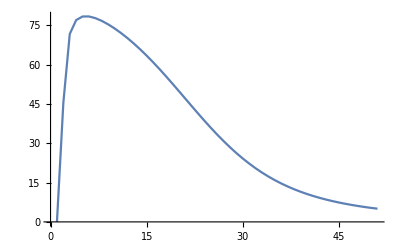

{1.,-1.11267×10^-15,2.,45.5133,3.,71.7076,4.,77.0027,5.,78.3682,6.,78.379,7.,77.7313,8.,76.6838,9.,75.3524,10.,73.7951,11.,72.0441,12.,70.1184,13.,68.0313,14.,65.7937,15.,63.4166,16.,60.9121,17.,58.2949,18.,55.5828,19.,52.7961,20.,49.9582,21.,47.0946,22.,44.232,23.,41.3971,24.,38.6161,25.,35.9127,26.,33.3078,27.,30.8189,28.,28.4593,29.,26.2384,30.,24.1614,31.,22.2304,32.,20.4442,33.,18.7992,34.,17.2897,35.,15.9089,36.,14.6488,37.,13.501,38.,12.4571,39.,11.5085,40.,10.6469,41.,9.86458,42.,9.1541,43.,8.50863,44.,7.92185,45.,7.388,46.,6.90183,47.,6.4586,48.,6.05402,49.,5.68424,50.,5.34581,51.,5.03562}

```mathematica
Nplot2 = ListLinePlot[MeanPhoton2,PlotRange->All]
Ndata2 = Cases[Nplot2, Line[p_]:>p,Infinity]//Flatten
```

```mathematica
Q=((71.70761046109068)-(8.293599388259013)^2-(8.293599388259013))/8.293599388259013
```

-0.647461

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
Inversion0=Sum[⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩-⟨Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]⟩,{n,0,10}]/.Calling
```

-ρ[1,1][t]+ρ[2,2][t]-ρ[4,4][t]+ρ[5,5][t]-ρ[7,7][t]+ρ[8,8][t]-ρ[10,10][t]+ρ[11,11][t]-ρ[13,13][t]+ρ[14,14][t]-ρ[16,16][t]+ρ[17,17][t]-ρ[19,19][t]+ρ[20,20][t]-ρ[22,22][t]+ρ[23,23][t]-ρ[25,25][t]+ρ[26,26][t]-ρ[28,28][t]+ρ[29,29][t]-ρ[31,31][t]+ρ[32,32][t]

```mathematica
Inversion1=Table[ρ[2,2][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[5,5][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[8,8][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Inversion2=Table[ρ[11,11][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[14,14][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[17,17][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Inversion3=Table[ρ[20,20][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[23,23][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[26,26][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Inversion4=Table[ρ[29,29][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[32,32][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Inversion5=-(Table[ρ[1,1][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[4,4][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[7,7][t]/.SSsol[Γ],{Γ,0,100}]);
```

```mathematica
Inversion6=-(Table[ρ[10,10][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[13,13][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[16,16][t]/.SSsol[Γ],{Γ,0,100}]);
```

```mathematica
Inversion7=-(Table[ρ[19,19][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[22,22][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[25,25][t]/.SSsol[Γ],{Γ,0,100}]);
```

```mathematica
Inversion8=-(Table[ρ[28,28][t]/.SSsol[Γ],{Γ,0,100}]+Table[ρ[31,31][t]/.SSsol[Γ],{Γ,0,100}]);
```

```mathematica
Inversion=Inversion1+Inversion2+Inversion3+Inversion4+Inversion5+Inversion6+Inversion7+Inversion8;
```

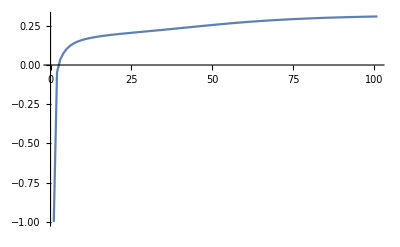

```mathematica
ListLinePlot[Inversion,PlotRange->All]
```

```mathematica
Inversion12=Table[ρ[2,2][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[5,5][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[8,8][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Inversion22=Table[ρ[11,11][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[14,14][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[17,17][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Inversion32=Table[ρ[20,20][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[23,23][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[26,26][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Inversion42=Table[ρ[29,29][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[32,32][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Inversion52=-(Table[ρ[1,1][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[4,4][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[7,7][t]/.SSsol[Γ],{Γ,0,4,0.1}]);
```

```mathematica
Inversion62=-(Table[ρ[10,10][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[13,13][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[16,16][t]/.SSsol[Γ],{Γ,0,4,0.1}]);
```

```mathematica
Inversion72=-(Table[ρ[19,19][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[22,22][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[25,25][t]/.SSsol[Γ],{Γ,0,4,0.1}]);
```

```mathematica
Inversion82=-(Table[ρ[28,28][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[ρ[31,31][t]/.SSsol[Γ],{Γ,0,4,0.1}]);
```

```mathematica
Inversionsmall=Inversion12+Inversion22+Inversion32+Inversion42+Inversion52+Inversion62+Inversion72+Inversion82;
```

```mathematica
Listsmall=Table[i,{i,0,4,0.1}];
```

```mathematica
InversionsmallRe=Transpose[{Listsmall,Inversionsmall}];
```

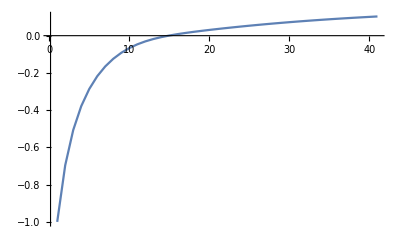

```mathematica
ListLinePlot[Inversionsmall,PlotRange->All]
```

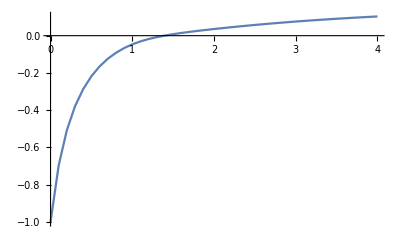

```mathematica
ListLinePlot[InversionsmallRe,PlotRange->All]
```

```mathematica
p1=ShowLegend[Show[ListLinePlot[Inversion,PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Γ[γ_12]","Inversion: Δ_12"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 10",Bold,25]}},LegendPosition->{0.5,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.3,0.1},LegendTextSpace->50}];
```

```mathematica
p2=ListLinePlot[InversionsmallRe,PlotStyle-> {{Directive[ CapForm["Round"],Blue,Thickness[0.012]]}},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]];
```

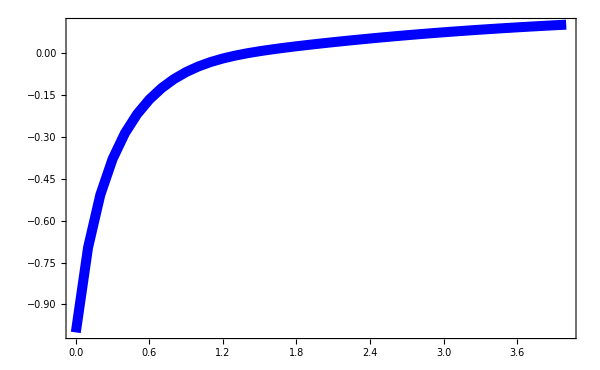

```mathematica
Show[Graphics[{Rectangle[{-7.2,-2.1},{8,9},p1],Rectangle[{0.5,0.5},{6.5,6.5},p2]}],ImageSize->{600,520}]
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
G[n_]:=(4 g^2)/(γ12+Γ+2 κ (n-1/2-√(n(n+1))));
```

```mathematica
Rst0=Sum[G[n]n⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩,{n,0,10}]-Sum[G[n](n+1)⟨Subscript[n, OverHat[1]]+1,Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]]+1,Subscript[1, OverHat[2]]⟩,{n,0,9}]/.Calling
```

-(4 ρ[4,4][t])/(0.99+Γ)+(4 ρ[5,5][t])/(0.981716+Γ)-(8 ρ[7,7][t])/(0.981716+Γ)+(8 ρ[8,8][t])/(0.98101+Γ)-(12 ρ[10,10][t])/(0.98101+Γ)+(12 ρ[11,11][t])/(0.980718+Γ)-(16 ρ[13,13][t])/(0.980718+Γ)+(16 ρ[14,14][t])/(0.980557+Γ)-(20 ρ[16,16][t])/(0.980557+Γ)+(20 ρ[17,17][t])/(0.980455+Γ)-(24 ρ[19,19][t])/(0.980455+Γ)+(24 ρ[20,20][t])/(0.980385+Γ)-(28 ρ[22,22][t])/(0.980385+Γ)+(28 ρ[23,23][t])/(0.980334+Γ)-(32 ρ[25,25][t])/(0.980334+Γ)+(32 ρ[26,26][t])/(0.980294+Γ)-(36 ρ[28,28][t])/(0.980294+Γ)+(36 ρ[29,29][t])/(0.980263+Γ)-(40 ρ[31,31][t])/(0.980263+Γ)+(40 ρ[32,32][t])/(0.980238+Γ)

```mathematica
Rst1=-Table[(4/(0.99+Γ))ρ[4,4][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(4/(0.9817157287525381+Γ))ρ[5,5][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst2=-Table[(8/(0.9817157287525381+Γ))ρ[7,7][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(8/(0.9810102051443365+Γ))ρ[8,8][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst3=-Table[(12/(0.9810102051443365+Γ))ρ[10,10][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(12/(0.980717967697245+Γ))ρ[11,11][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst4=-Table[(16/(0.980717967697245+Γ))ρ[13,13][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(16/(0.9805572809000084+Γ))ρ[14,14][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst5=-Table[(20/(0.9805572809000084+Γ))ρ[16,16][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(20/(0.98045548849896+Γ))ρ[17,17][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst6=-Table[(24/(0.9804554884989668+Γ))ρ[19,19][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(24/(0.980385186031842+Γ)) ρ[20,20][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst7=-Table[(28/(0.9803851860318428+Γ))ρ[22,22][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(28/(0.98033370452904+Γ)) ρ[23,23][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst8=-Table[(32/(0.9803337045290423+Γ))ρ[25,25][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(32/(0.98029437251522+Γ)) ρ[26,26][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst9=-Table[(36/(0.98029437251522+Γ))ρ[28,28][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(36/(0.980263340389897+Γ))ρ[29,29][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst10=-Table[(40/(0.980263340389897+Γ))ρ[31,31][t]/.SSsol[Γ],{Γ,0,100,2}]+Table[(40/(0.98023823036596+Γ))ρ[32,32][t]/.SSsol[Γ],{Γ,0,100,2}];
```

```mathematica
Rst=Rst1+Rst2+Rst3+Rst4+Rst5+Rst6+Rst7+Rst8+Rst9+Rst10;
```

```mathematica
Rsp0=Sum[G[n]⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩,{n,0,10}]/.Calling
```

(4 ρ[2,2][t])/(0.99+Γ)+(4 ρ[5,5][t])/(0.981716+Γ)+(4 ρ[8,8][t])/(0.98101+Γ)+(4 ρ[11,11][t])/(0.980718+Γ)+(4 ρ[14,14][t])/(0.980557+Γ)+(4 ρ[17,17][t])/(0.980455+Γ)+(4 ρ[20,20][t])/(0.980385+Γ)+(4 ρ[23,23][t])/(0.980334+Γ)+(4 ρ[26,26][t])/(0.980294+Γ)+(4 ρ[29,29][t])/(0.980263+Γ)+(4 ρ[32,32][t])/(0.980238+Γ)

```mathematica
Rsp1=Table[(4/(0.99+Γ))ρ[2,2][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.9817157287525381+Γ))ρ[5,5][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Rsp2=Table[(4/(0.9810102051443365+Γ))ρ[8,8][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.980717967697245+Γ))ρ[11,11][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Rsp3=Table[(4/(0.9805572809000084+Γ))ρ[14,14][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.9804554884989668+Γ))ρ[17,17][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Rsp3=Table[(4/(0.980385186031842+Γ))ρ[20,20][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.980333704529042+Γ))ρ[23,23][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Rsp4=Table[(4/(0.980294372515228+Γ))ρ[26,26][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.980263340389897+Γ))ρ[29,29][t]/.SSsol[Γ],{Γ,0,100}]+Table[(4/(0.980238230365969+Γ))ρ[32,32][t]/.SSsol[Γ],{Γ,0,100}];
```

```mathematica
Rsp=Rsp1+Rsp2+Rsp3+Rsp4;
```

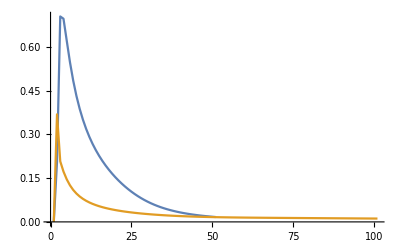

```mathematica
Rplot = ListLinePlot[{Rst,Rsp},PlotRange->All]
```

```mathematica
Rst12=-Table[(4/(0.99+Γ))ρ[4,4][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.9817157287525381+Γ))ρ[5,5][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst22=-Table[(8/(0.9817157287525381+Γ))ρ[7,7][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(8/(0.9810102051443365+Γ))ρ[8,8][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst32=-Table[(12/(0.98101020514433+Γ))ρ[10,10][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(12/(0.980717967697245+Γ))ρ[11,11][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst42=-Table[(16/(0.98071796769724+Γ))ρ[13,13][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(16/(0.9805572809000084+Γ))ρ[14,14][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst52=-Table[(20/(0.9805572809000084+Γ))ρ[16,16][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(20/(0.98045548849896+Γ))ρ[17,17][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst62=-Table[(24/(0.98045548849896+Γ))ρ[19,19][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(24/(0.980385186031842+Γ)) ρ[20,20][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst72=-Table[(28/(0.9803851860318428+Γ))ρ[22,22][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(28/(0.98033370452904+Γ)) ρ[23,23][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst82=-Table[(32/(0.9803337045290423+Γ))ρ[25,25][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(32/(0.98029437251522+Γ)) ρ[26,26][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst92=-Table[(36/(0.98029437251522+Γ))ρ[28,28][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(36/(0.980263340389897+Γ))ρ[29,29][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rst102=-Table[(40/(0.980263340389897+Γ))ρ[31,31][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(40/(0.98023823036596+Γ))ρ[32,32][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rstsmall=Rst12+Rst22+Rst32+Rst42+Rst52+Rst62+Rst72+Rst82+Rst92+Rst102;
```

```mathematica
Rsp12=Table[(4/(0.99+Γ))ρ[2,2][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.9817157287525381+Γ))ρ[5,5][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rsp22=Table[(4/(0.9810102051443365+Γ))ρ[8,8][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.980717967697245+Γ))ρ[11,11][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rsp32=Table[(4/(0.9805572809000084+Γ))ρ[14,14][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.980455488498966+Γ))ρ[17,17][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rsp32=Table[(4/(0.980385186031842+Γ))ρ[20,20][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.980333704529042+Γ))ρ[23,23][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rsp42=Table[(4/(0.980294372515228+Γ))ρ[26,26][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.980263340389897+Γ))ρ[29,29][t]/.SSsol[Γ],{Γ,0,4,0.1}]+Table[(4/(0.980238230365969+Γ))ρ[32,32][t]/.SSsol[Γ],{Γ,0,4,0.1}];
```

```mathematica
Rspsmall=Rsp12+Rsp22+Rsp32+Rsp42;
```

```mathematica
RstsmallRe=Transpose[{Listsmall,Rstsmall}];
```

```mathematica
RspsmallRe=Transpose[{Listsmall,Rspsmall}];
```

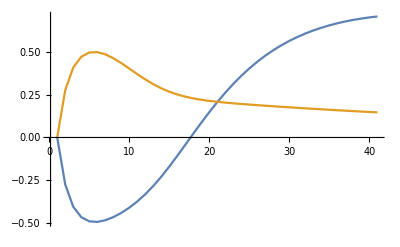

```mathematica
ListLinePlot[{Rstsmall,Rspsmall},PlotRange->All]
```

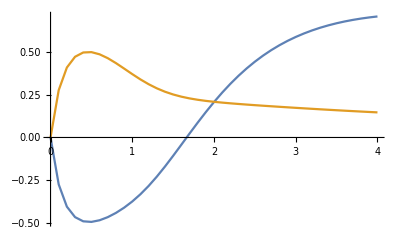

```mathematica
ListLinePlot[{RstsmallRe,RspsmallRe},PlotRange->All]
```

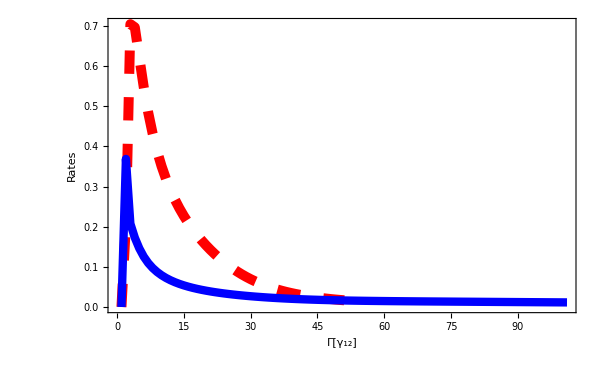

```mathematica
p3=ShowLegend[Show[ListLinePlot[{Rst,Rsp},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]},{Thickness[0.01],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","Rates"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]],Line[{{0,0.5},{4,0.5}}]}],Style["Stimulated",Bold,12]},
{Graphics[{Blue,Thickness[0.07],CapForm["Round"],Line[{{0,0.5},{4,0.5}}]}],Style["Spontaneous",Bold,12]}},LegendPosition->{-0.3,0.32},LegendBackground->White,LegendBorder->Black,LegendShadow->None,LegendSize->{0.52,0.15},LegendTextSpace->1.5},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 10",Bold,25]}},LegendPosition->{0.5,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.25,0.1},LegendTextSpace->50}]
```

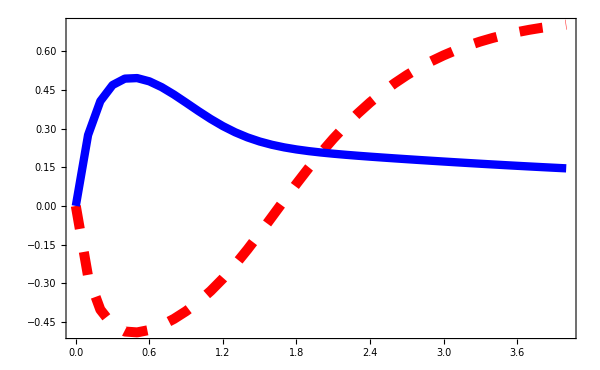

```mathematica
p4=Show[ListLinePlot[{RstsmallRe,RspsmallRe},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]},{Thickness[0.01],Blue}},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]]
```

```mathematica
Show[Graphics[{Rectangle[{-7,-4.1},{17,17},p3],Rectangle[{-0.4,-0.4},{10,10},p4]}],ImageSize->{600,520}]
```

-Graphics-

```mathematica
Rdata = Cases[Rplot, Line[p_]:>p,Infinity]//Flatten
```

{1.,1.05152×10^-16,2.,0.206198,3.,0.70424,4.,0.69645,5.,0.621595,6.,0.547653,7.,0.48447,8.,0.431808,9.,0.387801,10.,0.350639,11.,0.31886,12.,0.291338,13.,0.267212,14.,0.245823,15.,0.226668,16.,0.209354,17.,0.19358,18.,0.179111,19.,0.165769,20.,0.153413,21.,0.141938,22.,0.131264,23.,0.121329,24.,0.112086,25.,0.103495,26.,0.0955238,27.,0.0881428,28.,0.0813234,29.,0.075037,30.,0.0692548,31.,0.063947,32.,0.0590834,33.,0.0546334,34.,0.0505667,35.,0.0468534,36.,0.0434647,37.,0.040373,38.,0.0375522,39.,0.0349779,40.,0.0326273,41.,0.0304795,42.,0.0285154,43.,0.0267175,44.,0.0250698,45.,0.023558,46.,0.0221691,47.,0.0208915,48.,0.0197146,49.,0.0186289,50.,0.0176259,51.,0.0166981,1.,-1.50816×10^-17,2.,0.368689,3.,0.207582,4.,0.172528,5.,0.146045,6.,0.125444,7.,0.109576,8.,0.0971477,9.,0.0872007,10.,0.0790765,11.,0.0723217,12.,0.066618,13.,0.0617371,14.,0.0575117,15.,0.0538165,16.,0.050556,17.,0.0476563,18.,0.0450593,19.,0.0427187,20.,0.0405975,21.,0.0386655,22.,0.0368978,23.,0.035274,24.,0.0337772,25.,0.032393,26.,0.0311095,27.,0.0299165,28.,0.0288055,29.,0.0277689,30.,0.0268005,31.,0.0258948,32.,0.025047,33.,0.024253,34.,0.0235092,35.,0.0228123,36.,0.0221595,37.,0.021548,38.,0.0209757,39.,0.0204402,40.,0.0199395,41.,0.0194718,42.,0.0190353,43.,0.0186282,44.,0.0182488,45.,0.0178956,46.,0.0175671,47.,0.0172616,48.,0.0169777,49.,0.0167139,50.,0.0164689,51.,0.0162414,52.,0.0160299,53.,0.0158332,54.,0.0156501,55.,0.0154795,56.,0.0153201,57.,0.0151711,58.,0.0150312,59.,0.0148998,60.,0.0147757,61.,0.0146584,62.,0.0145469,63.,0.0144406,64.,0.014339,65.,0.0142413,66.,0.0141471,67.,0.0140559,68.,0.0139674,69.,0.013881,70.,0.0137965,71.,0.0137137,72.,0.0136321,73.,0.0135517,74.,0.0134722,75.,0.0133934,76.,0.0133153,77.,0.0132376,78.,0.0131603,79.,0.0130834,80.,0.0130066,81.,0.0129301,82.,0.0128537,83.,0.0127774,84.,0.0127012,85.,0.0126251,86.,0.0125491,87.,0.0124731,88.,0.0123972,89.,0.0123214,90.,0.0122457,91.,0.0121702,92.,0.0120947,93.,0.0120194,94.,0.0119443,95.,0.0118694,96.,0.0117946,97.,0.0117201,98.,0.0116459,99.,0.0115719,100.,0.0114982,101.,0.0114248}